### Constants

```mathematica
Clear [global]
```

```mathematica
h=6.62606896 10^-34;
hbar=h/(2Pi);
c=2.99792458 10^8;
kb=1.3806504 10^-23;
λNa=589.158 10^-9;
uB=9.27400968*10^-24;
Ahfs=h*885.81306440 10^6;
gS=2.0023193043622;
gL=0.99997613;
gI=-0.00080461080;
(*gJ=gL(J(J+1)-S(S+1)+L(L+1))/(2J(J+1))+gS(J(J+1)+S(S+1)-L(L+1))/(2J(J+1));*)
gJ=2.00229600;
gF=gJ(F(F+1)-I'(I'+1)+J(J+1))/(2F(F+1))+gI(F(F+1)+I'(I'+1)-J(J+1))/(2F(F+1));
gF'=gJ*(F'(F'+1)-I1(I1+1)+J(J+1))/(2F'(F'+1))+gI(F'(F'+1)+I1(I1+1)-J(J+1))/(2F'(F'+1));
```

### Breit-Rabi formula (for ground states)

#### States

```mathematica
I'=3/2;
J=1/2;
S=1/2;
L=0;
```

#### Hyperfine splitting

```mathematica
Ehfs[f_]=Ahfs/2(f(f+1)-I'(I'+1)-J(J+1));
ΔEhfs=Ahfs(I'+1/2)
```

1.17389×10^-24

#### Breit-Rabi formula (in terms of mJ and mI)

```mathematica
mJ=-1/2;
mI=-1/2;
E1[mj_,mi_,B_]=If[mi+mj==I'+1/2,((ΔEhfs I')/(2I'+1)+1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[mi+mj==-(I'+1/2),((ΔEhfs I')/(2I'+1)-1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[mj==1/2,(-ΔEhfs/(2(2I'+1))+gI uB (mi+mj)B/10000+ΔEhfs/2(1+(4(mi+mj))/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9),(-ΔEhfs/(2(2I'+1))+gI uB (mi+mj)B/10000-ΔEhfs/2(1+(4(mi+mj))/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9)]]];
Manipulate[Plot[{E1[1/2,3/2,B],E1[1/2,1/2,B],E1[1/2,-1/2,B],E1[1/2,-3/2,B],
E1[-1/2,3/2,B],E1[-1/2,1/2,B],E1[- 1/2,-1/2,B],E1[-1/2,-3/2,B]},{B,0,B0}],{{B0,1500},100,3000}]
```

#### Breit-Rabi formula (in terms of F and mF)

```mathematica
E2[f_,mf_,B_]=If[mf==I'+1/2,((ΔEhfs I')/(2I'+1)+1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[mf==-(I'+1/2),((ΔEhfs I')/(2I'+1)-1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[f==I'+1/2,(-ΔEhfs/(2(2I'+1))+gI uB mf B/10000+ΔEhfs/2(1+(4mf)/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9),(-ΔEhfs/(2(2I'+1))+gI uB mf B/10000-ΔEhfs/2(1+(4mf)/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9)]]];
Manipulate[Plot[{E2[1,1,B],E2[1,0,B],E2[1,-1,B],E2[2,2,B],
E2[2,1,B],E2[2,0,B],E2[2,-1,B],E2[2,-2,B]},{B,0,B0}],{{B0,1500},100,3000}]
```

#### Energy difference between F mF and F' mF states in ground states

```mathematica
B=350.5312929576195; (* Unit in Gauss*)

F=2;
mF=1;
F1=1;
mF'=0;

ΔE'=(E2[F,mF,B]-E2[F1,mF',B])*10^3    (* Unit in MHz*)
h % 10^6/kb 10^6(*Unit in μK*)

NSolve[2575.60637136==(E2[F,mF,Bb]-E2[F1,mF',Bb])*10^3,{Bb}]
```

2716.53

130373.

{{Bb→-858.548},{Bb→533.709}}

```mathematica
2578.9090985282073
```

2578.91

```mathematica
ΔE'[[1]]-ΔE'[[2]]
```

Part::partd: Part specification 1768.86⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1768.86⟦2⟧ is longer than depth of object.

1768.86⟦1⟧-1768.86⟦2⟧

```mathematica
listna=Table[{N[(E2[F,mF,bfield]-E2[F',mF',bfield])1000,20 ],bfield},{bfield,0.001,5,0.001}];
Export["d:/listna.txt",listna,"TSV"]
```

d:/listna.txt

```mathematica
63.696001390589394
```

63.696

245.57

196.89

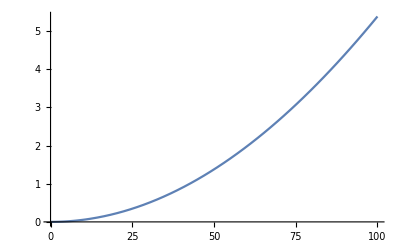

```mathematica
(E2[1,-1,352]-E2[1,0,352])*10^3
(E2[1,0,352]-E2[1,1,352])*10^3
Plot[(E2[1,-1,b]-E2[1,0,b])*10^3-(E2[1,0,b]-E2[1,1,b])*10^3,{b,0,100}]
```

#### Paschen-Back formula

-1151.17

-1426.9

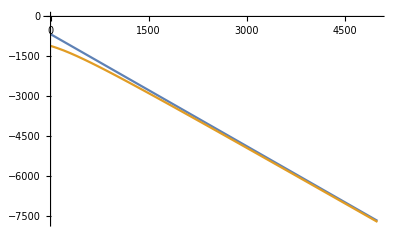

```mathematica
EPB[mi_,mj_,B1_]=Ahfs mi mj+uB(gJ mj+gI mi)B1/10000;
EPB[3/2,-1/2,347]/(h 10^6)
E2[1,1,347] 10^3
Plot[{EPB[3/2,-1/2,B]/(h 10^6),E2[1,1,B] 10^3},{B,0,5000}]
```

### Energy difference between 2,-2 state and 1,-1 state vs B field ( Unit in GHz )

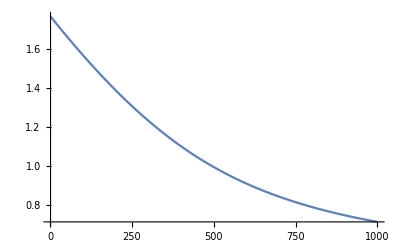

```mathematica
Ed[B2_]=E2[2,-2,B2]-E2[1,-1,B2];
Plot[Ed[B2],{B2,1,1000}]
```

```mathematica
Ed[0]
```

1.77163

```mathematica
E2[1,1,1]-E2[1,0,1]
```

-0.000701745

```mathematica
42.70000000000018
```

42.7

```mathematica
195.27031993302967-195.27072655567767
```

-0.000406623

```mathematica
195.3800778411201-195.38048423919662
```

-0.000406398

```mathematica
195.37005594066835
```

195.37